# QuissoCircuit Tutorial with Examples

Elementary usagepaclet:Q3/tutorial/QuissoCircuitUsage#1868432623 | Examples with Measurementspaclet:Q3/tutorial/QuissoCircuitUsage#1921589536
Grouping Circuit Elements With { }paclet:Q3/tutorial/QuissoCircuitUsage#188399535 | Examples with Controlled-U Gatespaclet:Q3/tutorial/QuissoCircuitUsage#580366830
More Complicated Gatespaclet:Q3/tutorial/QuissoCircuitUsage#2136908654 | Examples with Arbitrary Controlled-U Gatespaclet:Q3/tutorial/QuissoCircuitUsage#87721419
With Inputs and Outputspaclet:Q3/tutorial/QuissoCircuitUsage#94058740 | Matrix on QuissoCircuitpaclet:Q3/tutorial/QuissoCircuitUsage#462801707
Example with GraphStatespaclet:Q3/tutorial/QuissoCircuitUsage#175892259 | Matrix on QuissoCircuit: With Measurepaclet:Q3/tutorial/QuissoCircuitUsage#991141748

QuissoCircuit provides the graphical representation of the quantum circuits.

QuissoCircuit | Graphical representation of quantum circuit
Phase | Single-qubit phase gate (relative phase)
Rotation | Single-qubit rotation gate
EulerRotation | Single-qubit rotation gate specified by Euler angles
CNOT | Two-qubit controlled NOT gate
CZ | Two-qubit controlled Z gate
SWAP | Two-qubit SWAP gate
Toffoli | Three-qubit Toffoli gate
ControlledU | Multi-qubit controlled-U gate

Elements in the quantum circuit representation.

## Elementary usage

Elementary single qubit gates

```mathematica
<<Q3`Quisso`
```

```mathematica
Let[Qubit,S]
```

QuissoCircuit is a collection of quantum logic gates. Usually, it is displayed in a graphical form.

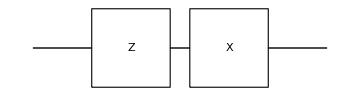

```mathematica
QuissoCircuit[S[1,3],S[1,1]]
```

Graphics directives can be used to change the style of labels of the quantum logic gates.

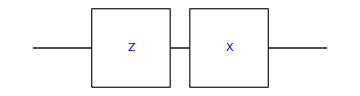

```mathematica
QuissoCircuit[Blue,S[1,3],S[1,1]]
```

0_S_10_S_2

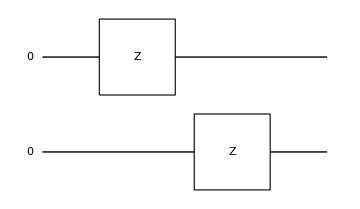

```mathematica
vec=LogicalForm[Ket[],S@{1,2}]
QuissoCircuit[vec,S[1,3],S[2,3]]
```

Here are all single-qubit gates displayed in a quantum circuit model.

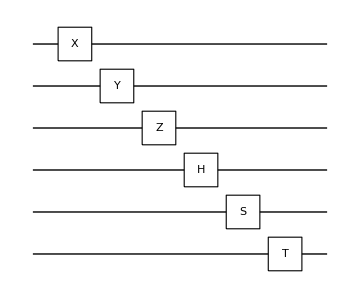

```mathematica
QuissoCircuit[S[1,1],S[2,2],S[3,3],S[4,6],S[5,7],S[6,8]]
```

“Spacer” is a special form to represent a time slice for no operation. It is useful for graphically extend certain time span. “Separator” puts a vertical dotted line to indicate a particular time slice.

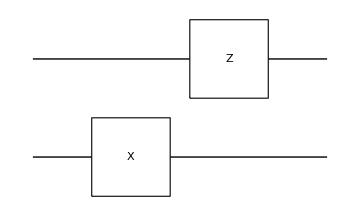

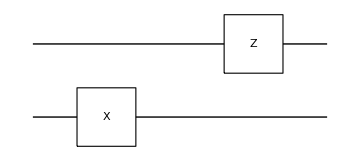

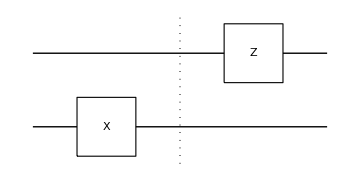

```mathematica
QuissoCircuit[S[2,1],S[1,3]]
QuissoCircuit[S[2,1],"Spacer",S[1,3]]
QuissoCircuit[S[2,1],"Separator",S[1,3]]
```

QuissoExpression converts QuissoCircuit to usual Quisso expressions.

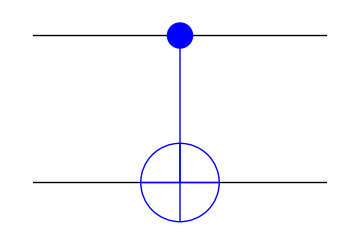

1/2-1/2 S_1^z S_2^x+S_1^z/2+S_2^x/2

```mathematica
qc=QuissoCircuit[Blue, CNOT[S[1],S[2]]]
QuissoExpression[qc]
```

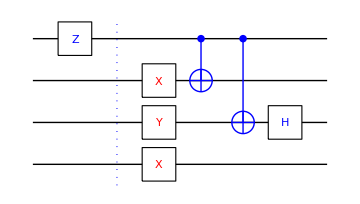

```mathematica
qc=QuissoCircuit[
Blue,S[1,3],"Separator",
{Red,S[2,1],S[3,2],S[4,1]},
{Blue, CNOT[S[1],S[2]] },
 CNOT[S[1],S[3]],
S[3,6]]
```

```mathematica
expr=S[3,6]**CNOT[S[1],S[3]]**CNOT[S[1],S[2]]**S[4,1]**S[3,2]**S[2,1]**S[1,3]//Garner
```

(ⅈ S_1^z S_4^x)/(2 √2)-(S_3^y S_4^x)/(2 √2)+(S_1^z S_3^y S_4^x)/(2 √2)-(ⅈ S_2^x S_3^x S_4^x)/(2 √2)+(ⅈ S_2^x S_3^z S_4^x)/(2 √2)-(ⅈ S_1^z S_2^x S_3^x S_4^x)/(2 √2)+(ⅈ S_1^z S_2^x S_3^z S_4^x)/(2 √2)-(ⅈ S_4^x)/(2 √2)

```mathematica
qcExpr=QuissoExpression[qc]
qcExpr-expr//Simplify
```

(ⅈ S_1^z S_4^x)/(2 √2)-(S_3^y S_4^x)/(2 √2)+(S_1^z S_3^y S_4^x)/(2 √2)-(ⅈ S_2^x S_3^x S_4^x)/(2 √2)+(ⅈ S_2^x S_3^z S_4^x)/(2 √2)-(ⅈ S_1^z S_2^x S_3^x S_4^x)/(2 √2)+(ⅈ S_1^z S_2^x S_3^z S_4^x)/(2 √2)-(ⅈ S_4^x)/(2 √2)

0

You can extend existing QuissoCircuit in a simple manner.

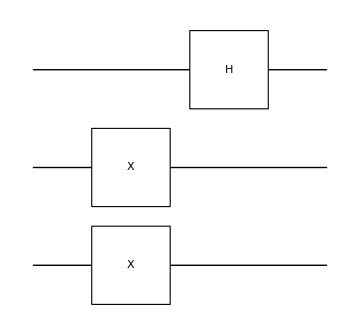

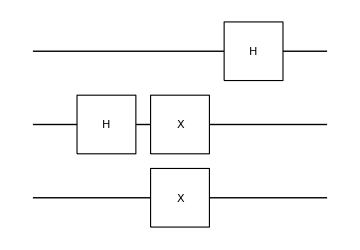

```mathematica
qc=QuissoCircuit[{S[2,1],S[3,1]},S[1,6]]
QuissoCircuit[S[2,6],qc]
```

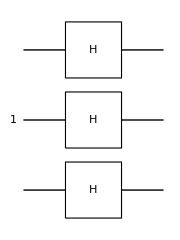

```mathematica
Clear[v]
nn=Range[1,3];
v[1]=Ket[S[2]->1];
QuissoCircuit[v[1],S[nn,6],ImageSize->Small]
```

0_S_10_S_20_S_3

0_S_1+1_S_1

0_S_2+1_S_2

0_S_3+1_S_3

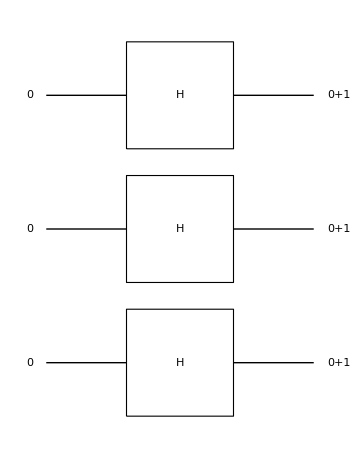

```mathematica
nn=Range[3];
v[1]=LogicalForm[Ket[],S[nn]]
v[2,1]=LogicalForm[Ket[]+Ket[S[1]->1]]
v[2,2]=LogicalForm[Ket[]+Ket[S[2]->1]]
v[2,3]=LogicalForm[Ket[]+Ket[S[3]->1]]
qc=QuissoCircuit[v[1],S[nn,6],v[2,1],v[2,2],v[2,3],
PlotRangePadding->{{0.5,1.5},None}]
```

```mathematica
expr=QuissoExpression[qc];
expr//LogicalForm
```

(0_S_10_S_20_S_3)/(2 √2)+(0_S_10_S_21_S_3)/(2 √2)+(0_S_11_S_20_S_3)/(2 √2)+(0_S_11_S_21_S_3)/(2 √2)+(1_S_10_S_20_S_3)/(2 √2)+(1_S_10_S_21_S_3)/(2 √2)+(1_S_11_S_20_S_3)/(2 √2)+(1_S_11_S_21_S_3)/(2 √2)

You can give custom labels.

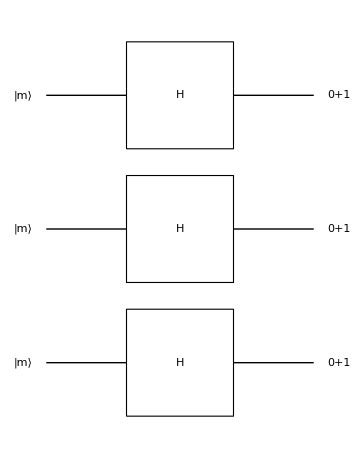

(0_S_10_S_20_S_3)/(2 √2)+(0_S_10_S_21_S_3)/(2 √2)+(0_S_11_S_20_S_3)/(2 √2)+(0_S_11_S_21_S_3)/(2 √2)+(1_S_10_S_20_S_3)/(2 √2)+(1_S_10_S_21_S_3)/(2 √2)+(1_S_11_S_20_S_3)/(2 √2)+(1_S_11_S_21_S_3)/(2 √2)

```mathematica
qc=QuissoCircuit[{v[1],"Label"->"|m⟩"},S[nn,6],v[2,1],v[2,2],v[2,3],
PlotRangePadding->{{0,1},None}]
expr=QuissoExpression@qc;LogicalForm@expr
```

If the custom label is a list, then its elements are rotated.

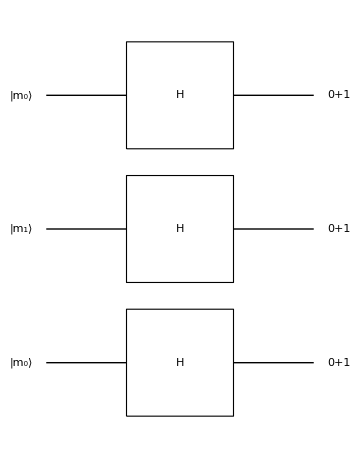

(0_S_10_S_20_S_3)/(2 √2)+(0_S_10_S_21_S_3)/(2 √2)+(0_S_11_S_20_S_3)/(2 √2)+(0_S_11_S_21_S_3)/(2 √2)+(1_S_10_S_20_S_3)/(2 √2)+(1_S_10_S_21_S_3)/(2 √2)+(1_S_11_S_20_S_3)/(2 √2)+(1_S_11_S_21_S_3)/(2 √2)

```mathematica
qc=QuissoCircuit[
{v[1],"Label"->{"|m_0⟩","|m_1⟩"}},
S[nn,6],v[2,1],v[2,2],v[2,3],
PlotRangePadding->{{0,1},None}]
expr=QuissoExpression@qc;
LogicalForm@expr
```

```mathematica
nn=Range[3];
v[1]=LogicalForm[Ket[],S[nn]]
v[2]=ProductState[S[nn]->{1,1}]
QuissoCircuit[v[1],S[nn,6],v[2],
PlotRangePadding->{{0,1},None}]
```

0_S_10_S_20_S_3

(0+1)_S_1⊗(0+1)_S_2⊗(0+1)_S_3

-Graphics-

Controlled-unitary gates

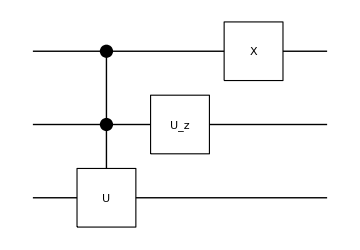

(1/8-ⅈ/16) (-3 ⅈ+√3) S_1^x S_2^z+1/16 (1-ⅈ √3) S_1^x S_3^y+1/16 ((-2-3 ⅈ)+(1+2 ⅈ) √3) S_1^y S_2^z+1/16 (ⅈ+√3) S_1^y S_3^y+1/16 ⅈ (ⅈ+√3) S_1^x S_2^z S_3^y+1/16 (-ⅈ-√3) S_1^y S_2^z S_3^y+1/16 ((3-2 ⅈ)+(6+ⅈ) √3) S_1^x+1/16 ((2+3 ⅈ)-(1+2 ⅈ) √3) S_1^y

(0 | 0 | 0 | 0 | 1/2 (-ⅈ+√3) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 (-ⅈ+√3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/4 (3+ⅈ √3) | 1/4 (-ⅈ-√3)
0 | 0 | 0 | 0 | 0 | 0 | 1/4 (ⅈ+√3) | 1/4 (3+ⅈ √3)
1/2 (-ⅈ+√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 (-ⅈ+√3) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 (ⅈ+√3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 (ⅈ+√3) | 0 | 0 | 0 | 0)

```mathematica
qc=QuissoCircuit[
ControlledU[S[{1,2}],Rotation[Pi/3,S[3,2],"Label"->"U"],"Label"->"R"],
Rotation[Pi/3,S[2,3]],
S[1,1]]
expr=QuissoExpression[qc]
mat=Simplify@Matrix[qc];
MatrixForm[mat]
```

## Grouping Circuit Elements With { }

In QuissoCircuitpaclet:Q3/ref/QuissoCircuit, Listpaclet:ref/List ({…}) can carry  two special meanings. First, it can put different quantum gates at the same time slice. Second, it can give options to particular quantum circuit elements.

```mathematica
<<Q3`Quisso`
```

```mathematica
Let[Qubit,S]
```

### Putting different quantum logic gates at the same time slice.

Here all quantum logic gates are displayed at different time slices (along the horizontal direction).

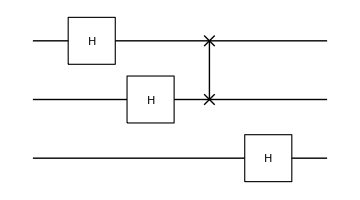

```mathematica
QuissoCircuit[S[1,6],S[2,6],SWAP[S[1],S[2]],S[3,6]]
```

Here the first two gates are displayed at the same time slice while others are separated long the time (horizontal) direction.

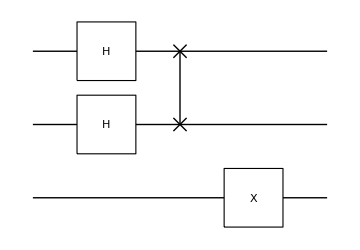

```mathematica
QuissoCircuit[{S[1,6],S[2,6]},SWAP[S[1],S[2]],S[3,1]]
```

Here the Hadamard gate and the SWAP gate are displayed at the same time slice. First of all, it results in a bad graphical representation. But, more importantly, it is physically wrong because the Hadamard gate and SWAP do not commute with each other. Only mutually commuting quantum logic gates are allowed to be grouped together in QuissoCircuit.

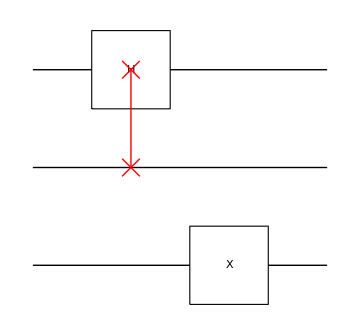

```mathematica
QuissoCircuit[{S[1,6],Red,SWAP[S[1],S[2]]},S[3,1]]
```

It is not allowed to group vectors with operators as they are completely different in character. For example, while the circuit model qc1 is okay, Q3 complains about qc2.

```mathematica
vec=LogicalForm[Ket[],S@{1,2}]
qc1=QuissoCircuit[vec,S[1,3],S[2,3]]
qc1=QuissoCircuit[{vec,S[1,3]},S[2,3]]
```

0_S_10_S_2

-Graphics-

-Graphics-

Here you can see grouping two vectors is allowed and generates an expected result.

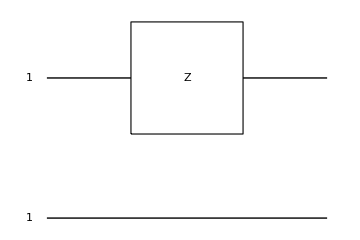

```mathematica
v=Ket[S[1]->1];
w=Ket[S[2]->1];
QuissoCircuit[{v,w},S[1,3]]
```

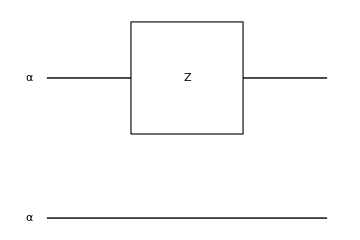

```mathematica
QuissoCircuit[{v,w,"Label"->Ket[α]},S[1,3]]
```

KNOWN BUG: This grouping feature does not work as expected when there is only a single grouping. For example, here two gates are supposed to be displayed at the same time slice, but apparently not. The bug will be fixed in a later release of Q3.

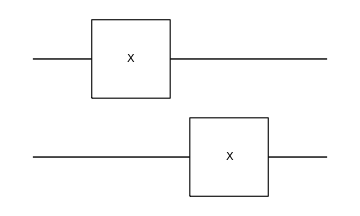

```mathematica
QuissoCircuit[{S[1,1],S[2,1]}]
```

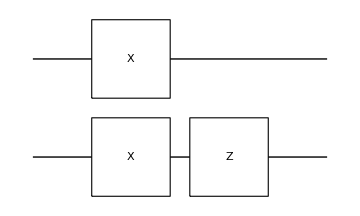

```mathematica
QuissoCircuit[{S[1,1],S[2,1]},S[2,3]]
```

### Giving options to particular quantum logic gates or input/output states

This is one of the simplest cases.

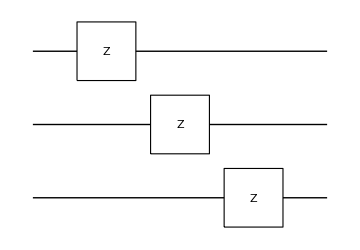

```mathematica
QuissoCircuit[S[1,3],S[2,3],S[3,3]]
```

In this example, the second and only the second gate is shown in red color.

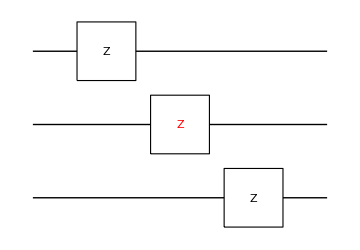

```mathematica
QuissoCircuit[S[1,3],{Red,S[2,3]},S[3,3]]
```

Unlike the example above, here all gates are displayed in red.

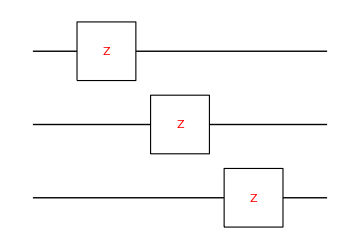

```mathematica
QuissoCircuit[Red,S[1,3],S[2,3],S[3,3]]
```

Here the second gate takes an option and it is labeled with “U” (not the default label “Z”).

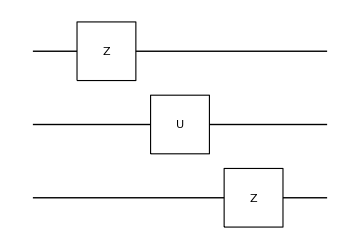

```mathematica
QuissoCircuit[S[1,3],{S[2,3],"Label"->"U"},S[3,3]]
```

## More Complicated Gates

```mathematica
<<Q3`Quisso`
```

```mathematica
Let[Qubit,S]
```

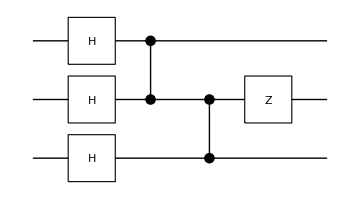

-Graphics-

{0.007297,Null}

{0.007053,Null}

-Graphics-

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
qc=QuissoCircuit[
S[{1,2,3},6],
CZ[S[1],S[2]],
CZ[S[2],S[3]],
S[2,3]
]
expr=QuissoExpression[qc]
Timing[mat1=Matrix[qc];]
Timing[mat2=Matrix[qc];]
mat2//MatrixForm
mat1-mat2//MatrixForm
```

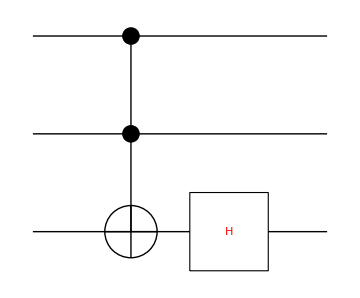

```mathematica
qc=QuissoCircuit[
Toffoli[S[1],S[2],S[3]],
Red,S[3,6]
]
```

```mathematica
qcExpr=QuissoExpression[qc]//Simplify
expr=S[3,6]**Toffoli[S[1],S[2],S[3]]//Simplify
qcExpr-expr//Simplify
```

1/(4 √2)(1+S_1^z S_2^z+S_1^z S_3^x-ⅈ S_1^z S_3^y+S_1^z S_3^z+S_2^z S_3^x-ⅈ S_2^z S_3^y+S_2^z S_3^z-S_1^z S_2^z S_3^x+ⅈ S_1^z S_2^z S_3^y-S_1^z S_2^z S_3^z-S_1^z-S_2^z+3 S_3^x+ⅈ S_3^y+3 S_3^z)

1/8 (√2+√2 S_1^z S_2^z+√2 S_1^z S_3^x-ⅈ √2 S_1^z S_3^y+√2 S_1^z S_3^z+√2 S_2^z S_3^x-ⅈ √2 S_2^z S_3^y+√2 S_2^z S_3^z-√2 S_1^z S_2^z S_3^x+ⅈ √2 S_1^z S_2^z S_3^y-√2 S_1^z S_2^z S_3^z-√2 S_1^z-√2 S_2^z+ⅈ √2 S_3^y+6 S_3^H)

3/8 (√2 S_3^x+√2 S_3^z-2 S_3^H)

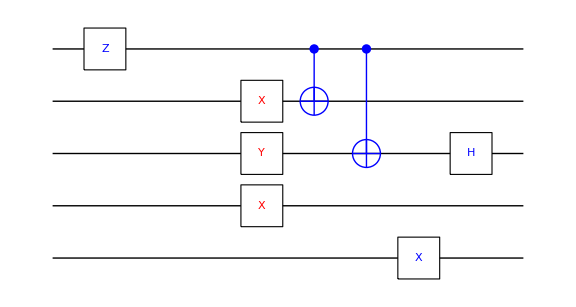

```mathematica
qc=QuissoCircuit[Blue,S[1,3],
"Spacer","Spacer",
{Red,S[2,1],S[3,2],S[4,1]},
{Blue, CNOT[S[1],S[2]] },
 CNOT[S[1],S[3]],
S[5,1],
S[3,6],
Opts->"A",
ImageSize->Large
]
```

```mathematica
qcExpr=QuissoExpression[qc]
expr=Multiply@@Reverse@{
S[1,3],S[2,1],S[3,2],S[4,1],CNOT[S[1],S[2]],CNOT[S[1],S[3]],S[5,1],S[3,6]}//Simplify
qcExpr-expr//Simplify
```

-(ⅈ S_4^x S_5^x)/(2 √2)+(ⅈ S_1^z S_4^x S_5^x)/(2 √2)-(S_3^y S_4^x S_5^x)/(2 √2)+(S_1^z S_3^y S_4^x S_5^x)/(2 √2)-(ⅈ S_2^x S_3^x S_4^x S_5^x)/(2 √2)+(ⅈ S_2^x S_3^z S_4^x S_5^x)/(2 √2)-(ⅈ S_1^z S_2^x S_3^x S_4^x S_5^x)/(2 √2)+(ⅈ S_1^z S_2^x S_3^z S_4^x S_5^x)/(2 √2)

-1/(2 √2)ⅈ (S_4^x S_5^x-S_1^z S_4^x S_5^x-ⅈ S_3^y S_4^x S_5^x+ⅈ S_1^z S_3^y S_4^x S_5^x+S_2^x S_3^x S_4^x S_5^x-S_2^x S_3^z S_4^x S_5^x+S_1^z S_2^x S_3^x S_4^x S_5^x-S_1^z S_2^x S_3^z S_4^x S_5^x)

0

## With Inputs and Outputs

You can specifies input and output states.

```mathematica
<<Q3`Quisso`
```

```mathematica
Let[Qubit,S]
Let[Real,a,b,c]
```

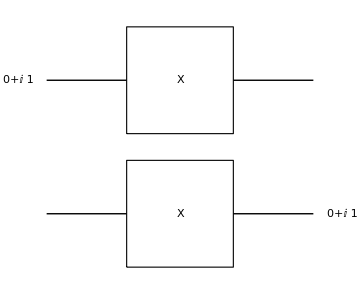

```mathematica
v1=Ket[]+I Ket[S[1]->1];
v2=Ket[]+I Ket[S[2]->1];
qc=QuissoCircuit[
{v1,"LabelSize"->0.5},
S[{1,2},1],
{v2,"LabelSize"->0.5},
PlotRangePadding->{1,0}]
```

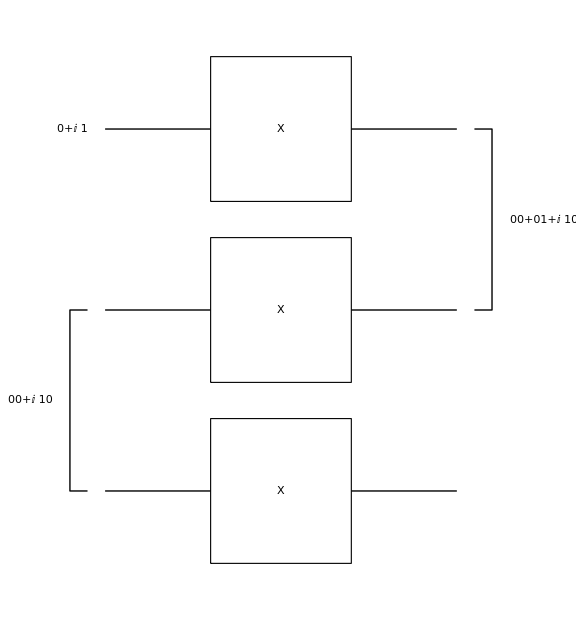

```mathematica
v3=LogicalForm[Ket[]+I Ket[S[1]->1]+Ket[S[2]->1],S[{1,2}]];
v4=LogicalForm[Ket[]+I Ket[S[2]->1],S[{2,3}]];
qc=QuissoCircuit[
{v1,v4,"LabelSize"->0.5},
{S[{1,2,3},1],"LabelSize"->0.5},
{v3,"LabelSize"->0.5},
PlotRangePadding->{1,0},
ImageSize->Large
]
```

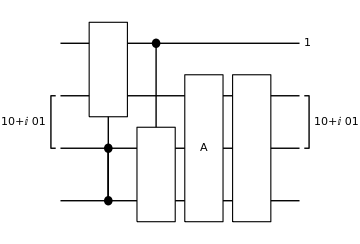

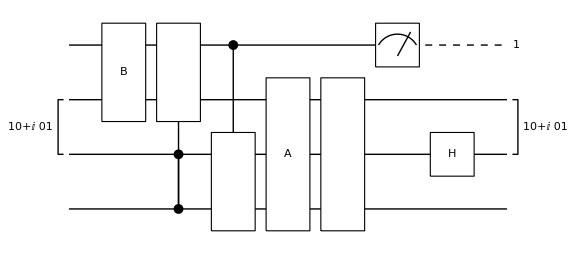

(1_S_1)/(2 √2)-(ⅈ 1_S_11_S_21_S_31_S_4)/(2 √2)+(ⅈ 1_S_11_S_2)/(2 √2)+(ⅈ 1_S_11_S_21_S_3)/(2 √2)+(ⅈ 1_S_11_S_21_S_4)/(2 √2)-(1_S_11_S_3)/(2 √2)-(1_S_11_S_31_S_4)/(2 √2)-(1_S_11_S_4)/(2 √2)

(0
0
0
0
0
0
0
0
1/(2 √2)
-1/(2 √2)
-1/(2 √2)
-1/(2 √2)
ⅈ/(2 √2)
ⅈ/(2 √2)
ⅈ/(2 √2)
-ⅈ/(2 √2))

```mathematica
Clear[expr,vec,mat];
expr[1]=S[2,1]+I S[4,3];
v1=Ket[S[2]->1]+ I Ket[S[3]->1];
mat[0]=ThePauli[1,3];
expr[2]=QuissoExpression[mat[0],S[{1,2}]];
qc=QuissoCircuit[v1,
ControlledU[S[{3,4}],S[1,1]-S[2,2]],
ControlledU[S[1],S[3,2]+I S[4,1]],
{expr[1],"Label"->"A"},
expr[1],{Ket[S[1]->1],v1}
]
qc=QuissoCircuit[{expr[2],"Label"->"B"},
qc,Measurement[S[1]],S[3,6],
ImageSize->Large]
expr[0]=QuissoExpression[qc]
vec[0]=Matrix[qc];
vec[0]//MatrixForm
```

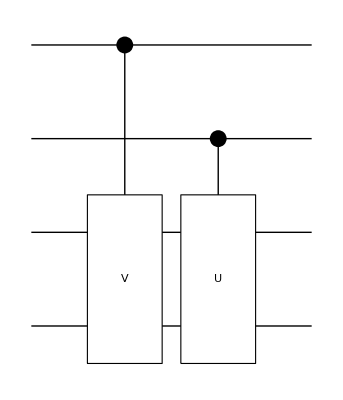

1/4+1/4 S_1^z S_2^z+1/2 ⅈ S_3^y S_4^x-1/2 S_1^z S_2^z S_3^y-1/2 ⅈ S_1^z S_2^z S_4^x-1/2 ⅈ S_1^z S_3^y S_4^x-1/2 ⅈ S_2^z S_3^y S_4^x+1/2 ⅈ S_1^z S_2^z S_3^y S_4^x+S_1^z/4+S_2^z/4+S_3^y/2+(ⅈ S_4^x)/2

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0)

```mathematica
expr[1]=S[2,1]+I S[4,3];
qc=QuissoCircuit[
ControlledU[S[1],S[3,2]+I S[4,1],"Label"->"V"],
ControlledU[S[2],S[3,2]+I S[4,1],"Label"->"U"],
ImageSize->Automatic
]
expr[0]=QuissoExpression[qc]
mat[0]=Matrix[qc];
mat[0]//MatrixForm
```

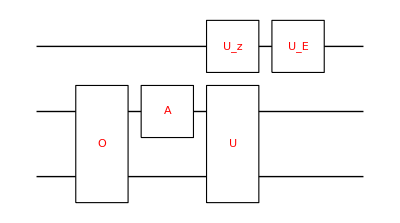

1/2 ⅈ (ⅈ+√3) Cos[b/2] Cos[1/2 (a+c+ϕ)] S_2^z+1/2 (ⅈ+√3) Cos[1/2 (a-c-ϕ)] S_1^y S_2^z Sin[b/2]-1/2 (ⅈ+√3) S_1^x S_2^z Sin[b/2] Sin[1/2 (a-c-ϕ)]-1/2 S_1^x S_2^x S_4^z Sin[b/2] (2 (1+(-1)^(1/3)) Cos[ϕ/2] Sin[(a-c)/2]+(-3-ⅈ √3) Cos[(a-c)/2] Sin[ϕ/2])+1/2 Cos[b/2] S_1^z S_2^x S_4^z (2 (1+(-1)^(1/3)) Cos[ϕ/2] Sin[(a+c)/2]+(3+ⅈ √3) Cos[(a+c)/2] Sin[ϕ/2])+1/2 S_1^y S_2^x S_4^z Sin[b/2] (2 (1+(-1)^(1/3)) Cos[(a-c)/2] Cos[ϕ/2]+(3+ⅈ √3) Sin[(a-c)/2] Sin[ϕ/2])+1/2 Cos[b/2] S_2^x S_4^z (2 (ⅈ+(-1)^(5/6)) Cos[(a+c)/2] Cos[ϕ/2]+(-3 ⅈ+√3) Sin[(a+c)/2] Sin[ϕ/2])+1/2 (ⅈ+√3) Cos[b/2] S_1^z S_2^z Sin[1/2 (a+c+ϕ)]

(1/2 (ⅈ+√3) Cos[b/2] (ⅈ Cos[1/2 (a+c+ϕ)]+Sin[1/2 (a+c+ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)]) | 0
0 | 1/2 (ⅈ+√3) Cos[b/2] (ⅈ Cos[1/2 (a+c+ϕ)]+Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)])
-1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (ⅈ+√3) Sin[b/2] (ⅈ Cos[1/2 (a-c-ϕ)]+Sin[1/2 (a-c-ϕ)]) | 0
0 | 1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (ⅈ+√3) Sin[b/2] (ⅈ Cos[1/2 (a-c-ϕ)]+Sin[1/2 (a-c-ϕ)])
1/2 ⅈ (ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 ⅈ (ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0
0 | 1/2 ⅈ (ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 ⅈ (ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)])
-1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (1-ⅈ √3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0
0 | 1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (1-ⅈ √3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]))

```mathematica
Let[Real,ϕ]
qc=QuissoCircuit[
Red,{expr[1],"Label"->"O"},
Phase[Pi/3,S[2],"Label"->"A"],
{Rotation[ϕ,S[1,3]],
{expr[1],"Label"->"U"}},
EulerRotation[{a,b,c},S[1]],
ImageSize->Automatic
]
expr[0]=QuissoExpression[qc]
mat[0]=Simplify@Matrix[qc];
mat[0]//MatrixForm
```

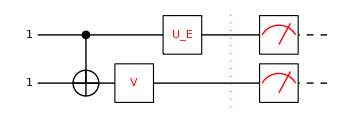

```mathematica
Let[Real,ϕ,a,b,c]
expr[1]=S[2,1]+I S[3,3];
qc=QuissoCircuit[
Ket[S[{1,2}]->1],
CNOT[S[1],S[2]],Red,
Rotation[ϕ,S[2,3],"Label"->"V"],
EulerRotation[{a,b,c},S[1]],
"Separator",
Measurement[S[{1,2}]]
]
```

```mathematica
expr[0]=QuissoExpression[qc]
vec[0]=Simplify@Matrix[qc];
vec[0]//MatrixForm
```

Measurement::nonum: Cannot perform a measurement on a non-numeric state vector. Probability half is assumed.

-(␣ Sin[b/2] (Cos[1/2 (a-c+ϕ)]-ⅈ Sin[1/2 (a-c+ϕ)]))/(|Sin[b/2]|)

Measurement::nonum: Cannot perform a measurement on a non-numeric state vector. Probability half is assumed.

(-(Sin[b/2] (Cos[1/2 (a-c+ϕ)]-ⅈ Sin[1/2 (a-c+ϕ)]))/(|Sin[b/2]|)
0
0
0)

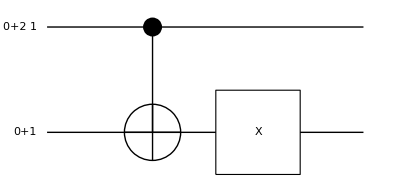

␣+2 1_S_1+2 1_S_11_S_2+1_S_2

(1
1
2
2)

```mathematica
qc=QuissoCircuit[
ProductState[S[1]->{1,2},S[2]->{1,1}],
CNOT[S[1],S[2]],
S[2,1],
ImageSize->Automatic
]
expr[0]=QuissoExpression[qc]
vec[0]=Matrix[qc];
vec[0]//MatrixForm
```

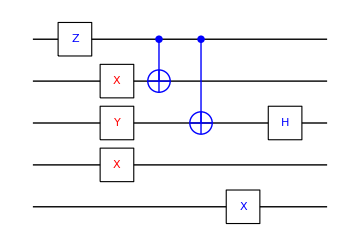

```mathematica
qc=QuissoCircuit[Blue,S[1,3],
{Red,S[2,1],S[3,2],S[4,1]},
{Blue, CNOT[S[1],S[2]] },
 CNOT[S[1],S[3]],
S[5,1],
S[3,6],
Opts->"A"
]
```

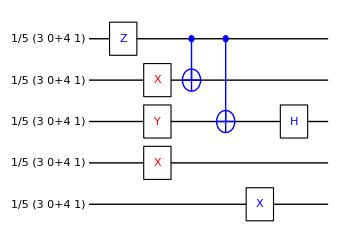

-Graphics-

{-(96 ⅈ √2)/3125,-(72 ⅈ √2)/3125,-(72 ⅈ √2)/3125,-(54 ⅈ √2)/3125,-(672 ⅈ √2)/3125,-(504 ⅈ √2)/3125,-(504 ⅈ √2)/3125,-(378 ⅈ √2)/3125,-(72 ⅈ √2)/3125,-(54 ⅈ √2)/3125,-(54 ⅈ √2)/3125,-(81 ⅈ)/(3125 √2),-(504 ⅈ √2)/3125,-(378 ⅈ √2)/3125,-(378 ⅈ √2)/3125,-(567 ⅈ)/(3125 √2),(96 ⅈ √2)/3125,(72 ⅈ √2)/3125,(72 ⅈ √2)/3125,(54 ⅈ √2)/3125,-(672 ⅈ √2)/3125,-(504 ⅈ √2)/3125,-(504 ⅈ √2)/3125,-(378 ⅈ √2)/3125,(128 ⅈ √2)/3125,(96 ⅈ √2)/3125,(96 ⅈ √2)/3125,(72 ⅈ √2)/3125,-(896 ⅈ √2)/3125,-(672 ⅈ √2)/3125,-(672 ⅈ √2)/3125,-(504 ⅈ √2)/3125}

```mathematica
qc=QuissoCircuit[
ProductState[S[{1,2,3,4,5}]->{3,4}/5],
Blue,S[1,3],
{Red,S[2,1],S[3,2],S[4,1]},
{Blue, CNOT[S[1],S[2]] },
 CNOT[S[1],S[3]],
S[5,1],S[3,6],
PlotRangePadding->{{2,0},0}
]
expr[0]=QuissoExpression[qc]
vec[0]=Simplify@Matrix[qc];
vec[0]//Normal
```

## Example with GraphStates

```mathematica
<<Q3`Quisso`
```

```mathematica
Let[Qubit,S]
```

Let us consider the graph states.



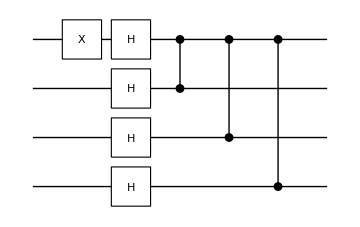

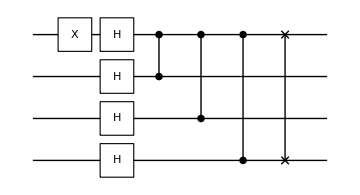

-Graphics-

```mathematica
g=Graph[{S[1]<->S[2],S[1]<->S[3],S[1]<->S[4]}]
qc=QuissoCircuit[S[1,1],g]
qc=QuissoCircuit[qc,SWAP[S[1],S[4]]]
Elaborate@QuissoExpression[qc]//Simplify
```

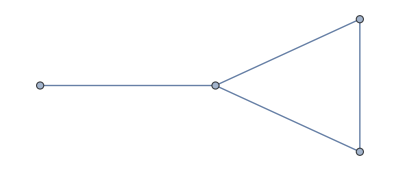

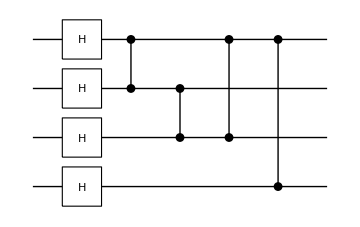

```mathematica
g=Graph[{S[1]<->S[2],S[2]<->S[3],S[1]<->S[3],S[1]<->S[4]}]
QuissoCircuit[g]
```

0_S_10_S_20_S_30_S_4

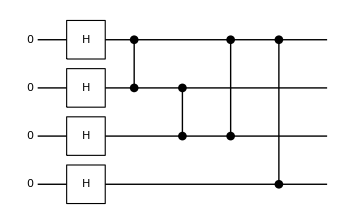

␣/4-1/4 1_S_11_S_2-1/4 1_S_11_S_21_S_3+(1_S_1)/4+1/4 1_S_11_S_21_S_31_S_4+1/4 1_S_11_S_21_S_4-1/4 1_S_11_S_3+1/4 1_S_11_S_31_S_4-1/4 1_S_11_S_4-1/4 1_S_21_S_3-1/4 1_S_21_S_31_S_4+(1_S_2)/4+1/4 1_S_21_S_4+(1_S_3)/4+1/4 1_S_31_S_4+(1_S_4)/4

{1/4,1/4,1/4,1/4,1/4,1/4,-1/4,-1/4,1/4,-1/4,-1/4,1/4,-1/4,1/4,-1/4,1/4}

1/4 (␣+1_S_1-1_S_11_S_2-1_S_11_S_21_S_3+1_S_11_S_21_S_31_S_4+1_S_11_S_21_S_4-1_S_11_S_3+1_S_11_S_31_S_4-1_S_11_S_4+1_S_2-1_S_21_S_3-1_S_21_S_31_S_4+1_S_21_S_4+1_S_3+1_S_31_S_4+1_S_4)

0

```mathematica
in=LogicalForm[Ket[],S[{1,2,3,4}]]
qc=QuissoCircuit[in,g]
v[1]=QuissoExpression[qc]
v[2]=Matrix[qc];
v[2]//Normal
v[3]=GraphState[g]
v[1]-v[3]//Simplify//Normal
```

## Examples with Measurements

Here are simple examples with measurements.

```mathematica
<<Q3`Quisso`
```

```mathematica
Let[Qubit,S]
```

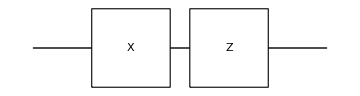

-1_S_1

```mathematica
qc=QuissoCircuit[Ket[],S[1,1],S[1,3]]
ex=QuissoExpression[qc]
```

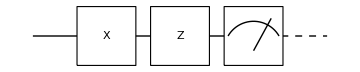

-1_S_1

```mathematica
qc=QuissoCircuit[Ket[],S[1,1],S[1,3],Measurement[S[1]]]
ex=QuissoExpression[qc]
```

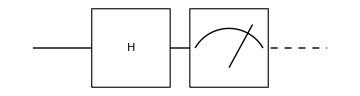

1_S_1

```mathematica
qc=QuissoCircuit[Ket[],S[1,6],Measurement[S[1]]]
ex=QuissoExpression[qc]
```

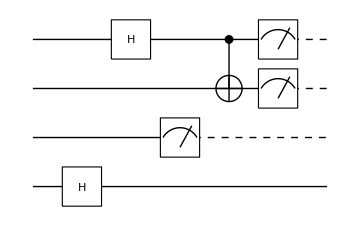

```mathematica
qc=QuissoCircuit[
Ket[],
S[4,6],S[1,6],
Measurement[S[3]],
CNOT[S[1],S[2]],
Measurement[S@{1,2}]
]
```

```mathematica
cc=(QuissoExpression@qc)//Simplify;
ccc=LogicalForm[cc,S[{1,2,3,4}]]
QuissoFactor[ccc,S[{1,2}]]
```

(1_S_11_S_20_S_30_S_4+1_S_11_S_20_S_31_S_4)/(√2)

1_S_11_S_2⊗((0_S_30_S_4+0_S_31_S_4)/(√2))

Take another example

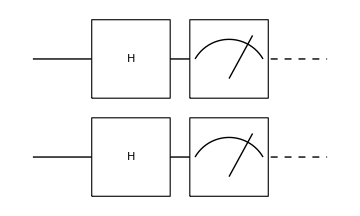

```mathematica
qc=QuissoCircuit[Ket[],{S[1,6],S[2,6]},Measurement[S[{1,2}]]]
```

```mathematica
data=Table[(result=QuissoExpression[qc];Readout[result,S[{1,2}]]),{200}];
Histogram3D[data,AxesLabel->{S[1,],S[2,],"Counts"}]
```

-Graphics3D-

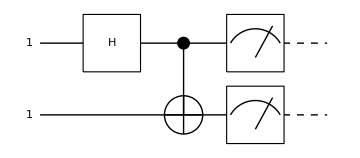

```mathematica
qc=QuissoCircuit[
Ket[S[{1,2}]->1],
S[1,6],CNOT[S[1],S[2]],
{Measurement[S[1]],Measurement[S[2]]}
]
```

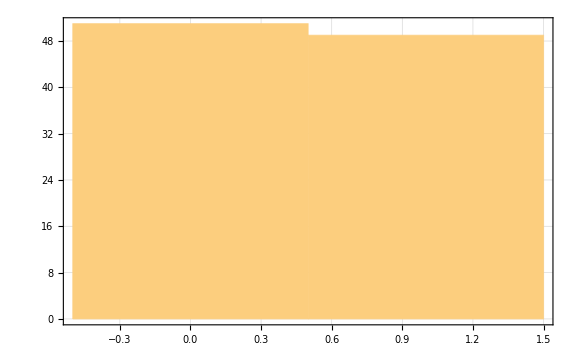

```mathematica
data=Table[(result=QuissoExpression[qc];Readout[result,S[1]]),{100}];
Histogram[data,Axes->False,Frame->True,FrameStyle->Large]
```

(0_S_11_S_2-1_S_10_S_2)/(√2)

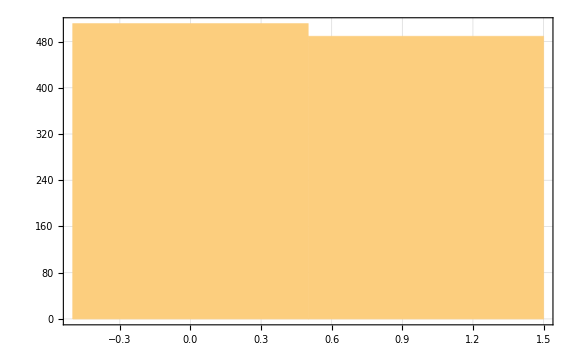

```mathematica
v=QuissoCNOT[S[1],S[2]]**S[1,6]**Ket[S[{1,2}]->1]//Simplify;
v//LogicalForm
data=Table[
u=Measurement[Measurement[v,S[2]],S[1]];
Readout[u,S[1]],
{j,1000}
];
Histogram[data]
```

## Examples with Controlled-U Gates

```mathematica
<<Q3`Quisso`
```

Here are simple examples involving controlled-U gates.

```mathematica
Let[Qubit,S]
```

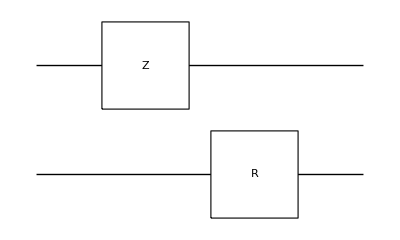

```mathematica
QuissoCircuit[
S[1,3],
Rotation[Pi/3,S[2,1],"Label"->"R"],
ImageSize->Automatic]
```

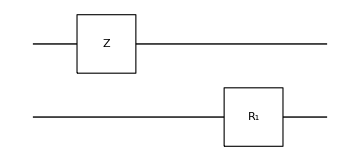

```mathematica
qc=QuissoCircuit[
S[1,3],Pi,
Rotation[Pi/3,S[2,1],"Label"->"R_1"]]
```

```mathematica
qc//QuissoExpression
```

-1/2 ⅈ π S_1^z S_2^x+1/2 √3 π S_1^z

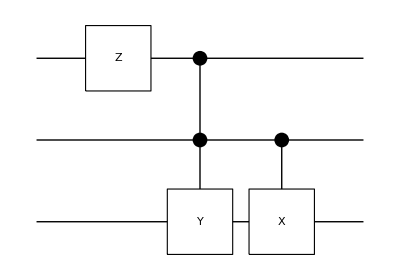

```mathematica
QuissoCircuit[
S[1,3],
ControlledU[S[{1,2}],S[3,2]],
ControlledU[S[2],S[3,1]],
ImageSize->Automatic
]
```

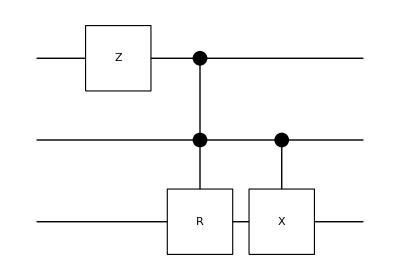

```mathematica
QuissoCircuit[
S[1,3],
ControlledU[S[{1,2}],Rotation[Pi/3,S[3,2]],"Label"->"R"],
ControlledU[S[2],S[3,1]],
ImageSize->Automatic
]
```

## Examples with Arbitrary Controlled-U Gates

```mathematica
<<Q3`Quisso`
```

```mathematica
Let[Qubit,S]
```

S_3^x-ⅈ S_3^y+S_4^z/2

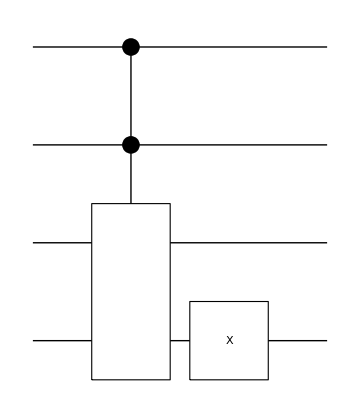

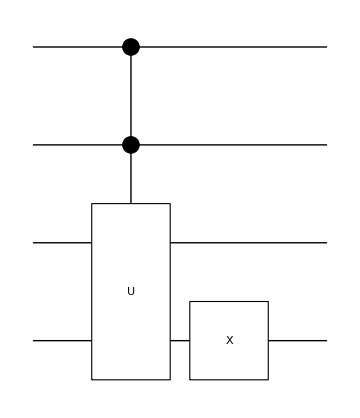

```mathematica
expr=S[3,1]- I S[3,2] + S[4,3]/2
qc1=QuissoCircuit[ControlledU[S[{1,2}],expr],S[4,1]]
qc2=QuissoCircuit[ControlledU[S[{1,2}],expr,"Label"->"U"],S[4,1]]
```

```mathematica
ex1=QuissoExpression[qc1]//Simplify
ex2=QuissoExpression[qc2]//Simplify
ex1-ex2//Simplify
```

1/8 (2 S_1^z S_4^x+ⅈ (S_1^z S_4^y-2 ⅈ S_2^z S_4^x+S_2^z S_4^y-2 ⅈ S_3^x S_4^x-2 S_3^y S_4^x+2 ⅈ S_1^z S_2^z S_4^x-S_1^z S_2^z S_4^y+2 ⅈ S_1^z S_3^x S_4^x+2 S_1^z S_3^y S_4^x+2 ⅈ S_2^z S_3^x S_4^x+2 S_2^z S_3^y S_4^x-2 ⅈ S_1^z S_2^z S_3^x S_4^x-2 S_1^z S_2^z S_3^y S_4^x-6 ⅈ S_4^x-S_4^y))

1/8 (2 S_1^z S_4^x+ⅈ (S_1^z S_4^y-2 ⅈ S_2^z S_4^x+S_2^z S_4^y-2 ⅈ S_3^x S_4^x-2 S_3^y S_4^x+2 ⅈ S_1^z S_2^z S_4^x-S_1^z S_2^z S_4^y+2 ⅈ S_1^z S_3^x S_4^x+2 S_1^z S_3^y S_4^x+2 ⅈ S_2^z S_3^x S_4^x+2 S_2^z S_3^y S_4^x-2 ⅈ S_1^z S_2^z S_3^x S_4^x-2 S_1^z S_2^z S_3^y S_4^x-6 ⅈ S_4^x-S_4^y))

0

Let us take another example, where the (multi-qubit) gate (operator) is expressed in an expression of Qubit operators.

```mathematica
Let[Qubit,S]
```

S_3^0+ⅈ S_4^x

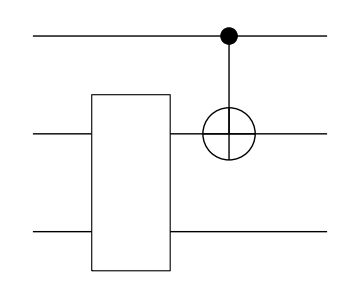

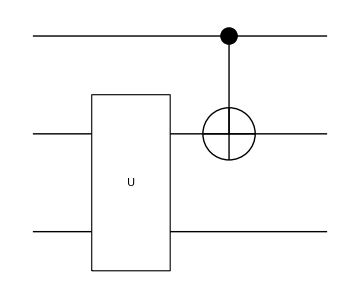

```mathematica
expr=S[3,0]+I S[4,1]
qc1=QuissoCircuit[ expr,CNOT[S[1],S[3]]]
qc2=QuissoCircuit[ {expr,"Label"->"U"},CNOT[S[1],S[3]]]
```

```mathematica
QuissoExpression[qc1]//Elaborate//Simplify
QuissoExpression[qc2]//Elaborate//Simplify
```

1/2 (1-S_1^z S_3^x+ⅈ S_1^z S_4^x+ⅈ S_3^x S_4^x-ⅈ S_1^z S_3^x S_4^x+S_1^z+S_3^x+ⅈ S_4^x)

1/2 (1-S_1^z S_3^x+ⅈ S_1^z S_4^x+ⅈ S_3^x S_4^x-ⅈ S_1^z S_3^x S_4^x+S_1^z+S_3^x+ⅈ S_4^x)

The gate is expressed in a matrix representation.

(ⅈ | 1
1 | -ⅈ)

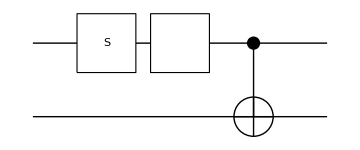

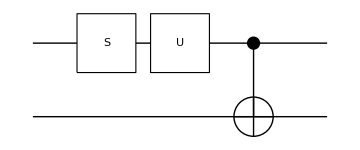

```mathematica
mat=ThePauli[1]+I ThePauli[3];
mat//MatrixForm
op=QuissoExpression[mat,S[1]];
qc1=QuissoCircuit[S[1,7], op,CNOT[S[1],S[3]]]
qc2=QuissoCircuit[ S[1,7],{op,"Label"->"U"},CNOT[S[1],S[3]]]
```

```mathematica
ex1=qc1//QuissoExpression//Elaborate//Simplify
ex2=qc2//QuissoExpression//Elaborate//Simplify
ex1-ex2//Simplify
```

1/2 (ⅈ+S_1^x S_3^x-ⅈ S_1^y S_3^x-S_1^z S_3^x+ⅈ S_1^x-S_1^y+ⅈ S_1^z+S_3^x)

1/2 (ⅈ+S_1^x S_3^x-ⅈ S_1^y S_3^x-S_1^z S_3^x+ⅈ S_1^x-S_1^y+ⅈ S_1^z+S_3^x)

0

Multi-qubit gate is expressed in a matrix representation.

(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)

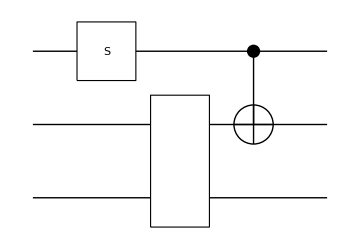

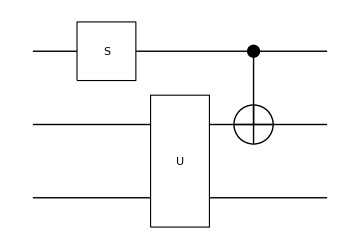

```mathematica
mat=ThePauli[1,2];
mat//MatrixForm
qq=S[{3,4}];
op=QuissoExpression[mat,qq];
qc1=QuissoCircuit[S[1,7], op,CNOT[S[1],S[3]]]
qc2=QuissoCircuit[ S[1,7],{op,"Label"->"U"},CNOT[S[1],S[3]]]
```

```mathematica
QuissoExpression[qc1]//Simplify
QuissoExpression[qc2]//Simplify
```

1/2 (-ⅈ S_1^z S_4^y+S_3^x S_4^y+S_1^z S_3^x S_4^y+ⅈ S_4^y)

1/2 (-ⅈ S_1^z S_4^y+S_3^x S_4^y+S_1^z S_3^x S_4^y+ⅈ S_4^y)

## Matrix on QuissoCircuit

Depending on the ratio of the “size” (the number of qubits) and the “depth” (the number of operations), Matrix is more efficient than the QuissoExpression.

```mathematica
<<Q3`Quisso`
```

```mathematica
Let[Qubit,S]
```

```mathematica
$N=5;
ss=S[Range[$N],None]
```

{S_1,S_2,S_3,S_4,S_5}

```mathematica
CP[j_,j_]:=S[j,6]
CP[j_,k_]:=ControlledU[S[j],
Phase[Pi Power[2,k-j],S[k],"Label"->Subscript["R",j-k]]
]/;j>k
CP[j_,k_]:=ControlledU[S[j],
Phase[Pi Power[2,j-k],S[k],"Label"->Subscript["R",k-j]]
]/;j<k
SW[j_]:=SWAP[S[j],S[$N-j+1]]
```

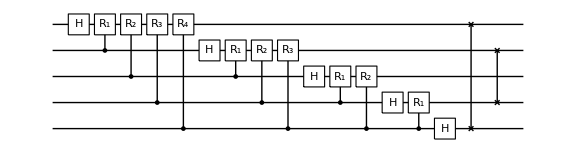

```mathematica
swaps=Table[SW[j],{j,1,$N/2}];
gates4a=Catenate@Table[CP[j,k],{k,1,$N},{j,k,$N}];
qft4a=Join[gates4a,swaps];
qc4a=QuissoCircuit[Sequence@@qft4a,ImageSize->Large]
```

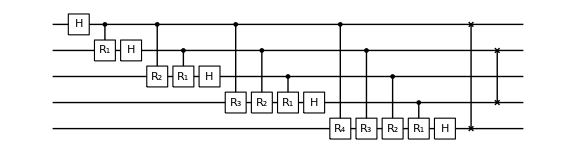

```mathematica
swaps=Table[SW[j],{j,1,$N/2}];
gates4b=Catenate@Table[CP[j,k],{k,1,$N},{j,1,k}];
qft4b=Join[gates4b,swaps];
qc4b=QuissoCircuit[Sequence@@qft4b,ImageSize->Large]
```

```mathematica
Timing[mat4a=Matrix[qc4a];]
Timing[mat4b=Matrix[qc4b];]
mat4a-mat4b//Simplify//Normal//Flatten//DeleteCases[#,0]&
Timing[mat4a=Matrix[qc4a];]
Timing[mat4b=Matrix[qc4b];]
mat4a-mat4b//Simplify//Normal//Flatten//DeleteCases[#,0]&
```

{0.719495,Null}

{0.654162,Null}

{}

{1.23733,Null}

{0.673492,Null}

{}

WARNING: The following takes quite long, sometime even fails, as the circuit is pretty deep compared with the size.

```mathematica
Timing[op4a=QuissoExpression[qc4a];]
```

{743.31,Null}

```mathematica
Timing[mat4c=Matrix[op4a];]
```

{0.371457,Null}

```mathematica
mat4a-mat4c//N//Chop//Normal
```

-Graphics-

## Matrix on QuissoCircuit: With Measure

Here we illustrate how Matrix works on a QuissoCircuitpaclet:Q3/ref/QuissoCircuit when it involves Measurementpaclet:Q3/ref/Measurement.

```mathematica
<<Q3`Quisso`
```

```mathematica
Let[Qubit,S]
```

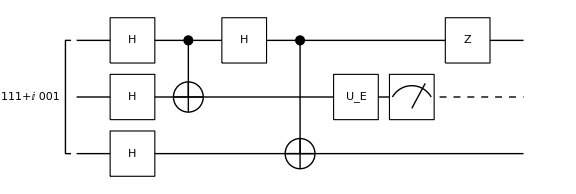

```mathematica
jj=Range[3];
ss=S[jj,None];
gg={Ket[ss->1]+I Ket[S[3]->1],
S[jj,6],
CNOT[S[1],S[2]],S[1,6],
CNOT[S[1],S[3]],
EulerRotation[{Pi/3,Pi/2,Pi/3},S[2]],
Measurement[S[2]],
S[1,3]};
qc=QuissoCircuit[Sequence@@gg,ImageSize->Large]
```

```mathematica
mat1=Matrix@qc//Simplify;
mat1//Normal
mat2=Matrix[QuissoExpression@qc,ss];
mat2//Normal
mat3=Matrix@qc//Simplify;
mat3//Normal
mat1-mat2//Simplify//Normal
mat2-mat3//Simplify//Normal
{Readout[QuissoExpression[mat1,ss],S[2]],
Readout[QuissoExpression[mat2,ss],S[2]]}
```

{((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),-((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),0,0,0,0,0,0}

{((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),-((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),0,0,0,0,0,0}

{((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),-((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),0,0,0,0,0,0}

{0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0}

{0,0}

Let us collect the measurement readouts to get the statistics.

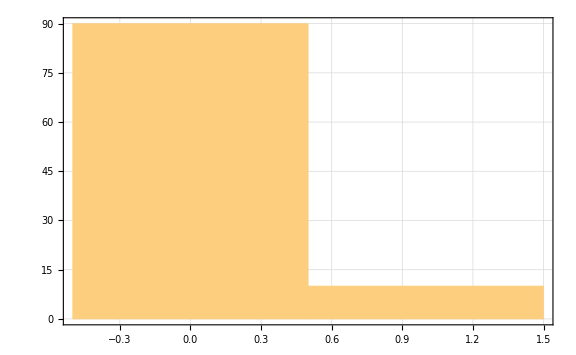

```mathematica
data1=Table[(
result=Matrix[qc];
Readout[QuissoExpression[result,ss],S[2]]
),100];
Histogram[data1]
```

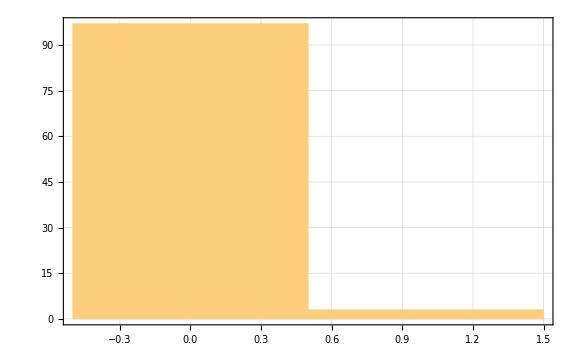

```mathematica
data2=Table[(result=QuissoExpression[qc];
Readout[result,S[2]]),100];
Histogram[data2]
```

Related Guides

Quisso

Related Tutorials

Quantum Teleportation

Quisso Quick Start